```mathematica
RSolve[{
l[2*k+1]==1/2+1/2*(l[2*k]+l[2*k+2]),
l[2*k+2]==1/2*(l[2*k+1]+l[2*k+3]),
l[0]==0,
l[m]==0},
l[k],k]
```

RSolve[{l[1+2 k]==1/2+1/2 (l[2 k]+l[2+2 k]),l[2+2 k]==1/2 (l[1+2 k]+l[3+2 k]),l[0]==0,l[m]==0},l[k],k]

```mathematica
a=({{1, 0, 0, 0, 0, 0, 0}, {-1/2, 1, -1/2, 0, 0, 0, 0}, {0, -1/2, 1, -1/2, 0, 0, 0}, {0, 0, -1/2, 1, -1/2, 0, 0}, {0, 0, 0, -1/2, 1, -1/2, 0}, {0, 0, 0, 0, -1/2, 1, -1/2}, {0, 0, 0, 0, 0, 0, 1}});
b=({{0}, {1/2}, {0}, {1/2}, {0}, {1/2}, {0}});
```

```mathematica
Solve[a.{x0,x1,x2,x3,x4,x5,x6}==b]
```

{{x0→0,x1→3/2,x2→2,x3→5/2,x4→2,x5→3/2,x6→0}}

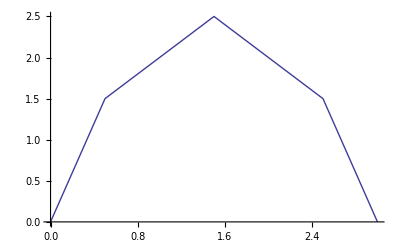

```mathematica
ListLinePlot[{{0,0},{1/2,3/2},{1,2},{3/2,5/2},{2,2},{5/2,3/2},{3,0}}]
```

```mathematica
Sum[2*i+1,{i, 0, k-1}]
```

k^2

```mathematica
Simplify[k^2+2*k+1]
```

(1+k)^2

```mathematica
b[k_]:=Piecewise[{{(Mod[k+1, 2]/2 + 1/2*b[k-1])/(1-1/2*(k-2)/(k-1)), k>2}, {1/2, k==2}}];
seq={#,b[#]}&/@Range[2,30]
beta[n_]=FindSequenceFunction[seq,n]
```

{{2,1/2},{3,1/3},{4,1},{5,4/5},{6,3/2},{7,9/7},{8,2},{9,16/9},{10,5/2},{11,25/11},{12,3},{13,36/13},{14,7/2},{15,49/15},{16,4},{17,64/17},{18,9/2},{19,81/19},{20,5},{21,100/21},{22,11/2},{23,121/23},{24,6},{25,144/25},{26,13/2},{27,169/27},{28,7},{29,196/29},{30,15/2}}

(1-(-1)^(-1+n)+2 (-1+n)-2 (-1)^(-1+n) (-1+n)+2 (-1+n)^2)/(8 n)

```mathematica
Simplify[beta[n], Assumptions->Mod[n,2]==1]
```

(-1+n)^2/(4 n)

```mathematica
2*2/(2*2+1)
```

4/5

```mathematica
Module[{m},
Simplify[(m*(m-1)+(m-1)^2)/(2*m-1)]
]
```

-1+m$31166

```mathematica
Simplify[(2 u^2-5 u+3)/(u-1)]
```

-3+2 u

```mathematica
Simplify[u/2+u*(u-2)-(u-2)^2-(u-2)]
```

-2+(3 u)/2

```mathematica
Simplify[1/2 u/2+1/2(3 u/2-2)]
```

-1+u

```mathematica
Clear[m];
h[k_]:=m/2+m*k-k^2-k
```

```mathematica
Simplify[1/2*h[k-1]+1/2*h[k]]
```

k (-k+m)

```mathematica
FullSimplify[(4*n^2+9*n+4)/(2*n+3)]
```

(4+n (9+4 n))/(3+2 n)

```mathematica
Simplify[
RSolve[{
x[k]==k/(k+1)*x[k+1]+(2*k+1)/2,
x[1]==m/2
},
x[k],k
],Assumptions->Element[k,Integers]&&k>0]
```

{{x[k]→-1/2 k (-2+EulerGamma+2 k-m+PolyGamma[0,k])}}

```mathematica
Simplify[(m-2)/(m-1)*m/2+m/2-1/4]
```

(1-7 m+4 m^2)/(4 (-1+m))

```mathematica
Simplify[(2*(m-2)+1)/(2*(m-2)+3)*m/2+2*(m-2+1)^2/(2*(m-1)+3)]
```

(4-13 m+24 m^2-12 m^3)/(2-8 m^2)

```mathematica
Simplify[(2*n+1)/(2*n+3)*(n+1)/2+(n+1)/2]
```

(2 (1+n)^2)/(3+2 n)

```mathematica
alpha[i_]:=(i-1)/i
```

```mathematica
Simplify[alpha[2*m-2]*alpha[2*m-1]*m/2+alpha[2*m-2]*beta[2*m-1]+beta[2*m-2],Assumptions->Element[m,Integers]&&m>0]
```

-2+(3 m)/2

```mathematica
Simplify[alpha[2*n+1+1]*beta[2*n+1+2]+beta[2*n+1+1],Assumptions->Element[n,Integers]&&n>0]
```

(2 (1+n)^2)/(3+2 n)

```mathematica
p[n_,x_]:=(2*n+1)/(2*n+3)*x+2*(n+1)^2/(2*n+3)
```

```mathematica
p[m-2,m/2]
```

(2 (-1+m)^2)/(3+2 (-2+m))+((1+2 (-2+m)) m)/(2 (3+2 (-2+m)))

```mathematica
Simplify[(2 (-1+m)^2)/(3+2 (-2+m))+((1+2 (-2+m)) m)/(2 (3+2 (-2+m)))]
```

-2+(3 m)/2

```mathematica
Simplify[(2*m-3)/(2*m-1)*m/2+2*(m-1)^2/(2*m-1)]
```

-2+(3 m)/2

```mathematica
Simplify[1/(2*(2*m-1))*(6*m^2-11*m+2)]
```

(2-11 m+6 m^2)/(-2+4 m)

```mathematica
RSolve[{
x[n]==(2*n+1)/(2*n+3)*x[n+1]+2*(n+1)^2/(2*n+3),
x[m-1]==m/2
},x[n],n]
```

{{x[n]→1/2 (m-2 n+2 m n-2 n^2)}}

```mathematica
RSolve[{
l[k]==1+1/2*(l[k-1]+l[k+1]),
l[0]==m/2,
l[m-1]==m/2
},l[k],k]
```

{{l[k]→1/2 (-2 k-2 k^2+m+2 k m)}}